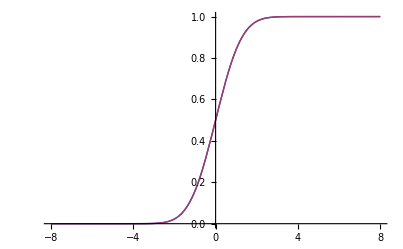

```mathematica
Plot[
{
CDF[NormalDistribution[],x],
Piecewise[
{{1,x>6},
{0,-x>6},
{approx1[x],0≤x≤1.87},
{1-approx1[-x],0≤-x≤1.87},
{approx2[x],1.87<x≤6},
{1-approx2[-x],1.87<-x≤6}}
]
},
{x,-8,8},
Filling->{1->{2}}]
```

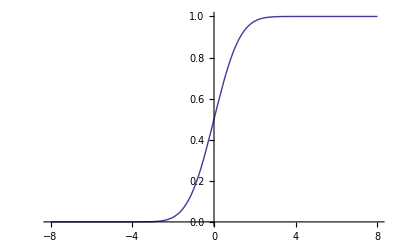

```mathematica
Plot[
{
CDF[NormalDistribution[],x]
},
{x,-8,8}]
```

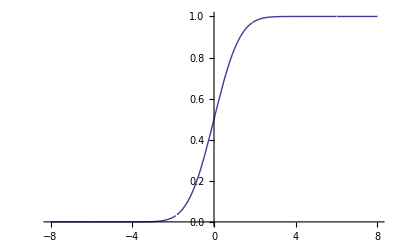

```mathematica
Plot[
{
Piecewise[
{{1,x>6},
{0,-x>6},
{approx1[x],0≤x≤1.87},
{1-approx1[-x],0≤-x≤1.87},
{approx2[x],1.87<x≤6},
{1-approx2[-x],1.87<-x≤6}}
]
},
{x,-8,8}]
```

```mathematica
Plot[
{
CDF[NormalDistribution[],x],
Piecewise[
{{1,x>6},
{0,-x>6},
{approx1[x],0≤x≤1.87},
{1-approx1[-x],0≤-x≤1.87},
{approx2[x],1.87<x≤6},
{1-approx2[-x],1.87<-x≤6}}
]
},
{x,-8,8},
Filling->{1->{2}}]
```

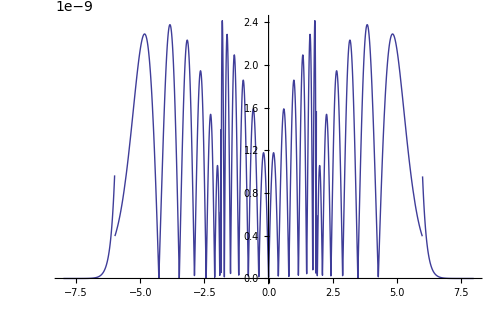

```mathematica
Plot[
{
Abs[CDF[NormalDistribution[],x]-
Piecewise[
{{1,x>6},
{0,-x>6},
{approx1[x],0≤x≤1.87},
{1-approx1[-x],0≤-x≤1.87},
{approx2[x],1.87<x≤6},
{1-approx2[-x],1.87<-x≤6}}
]]
},
{x,-8,8}]
```

```mathematica
approx1[x_]:=0.5+(x*(a0+(a1+a2*x^2)*x^2))/(1+(b1+(b2+b3*x^2)*x^2)*x^2)
```

```mathematica
approx2[x_]:=1.0-((c0+(c1+c2*x)*x)/(d0+(d1+(d2+d3*x)*x)*x))^16.0
```

```mathematica
a0:=0.398942270991;
a1:=0.020133760596;
a2:=0.002946756074;
b1:=0.217134277847;
b2:=0.018576112465;
b3:=0.000643163695;
c0:=1.398247031184;
c1:=-0.360040248231;
c2:=0.022719786588;
d0:=1.460954518699;
d1:=-0.305459640162;
d2:=0.038611796258;
d3:=-0.003787400686;
```